```mathematica
data=Import["C:\\Users\\Administrator\\Documents\\code\\Wolfram Mathematica\\2018建模模拟一\\Data.mat"];
```

```mathematica
d = Table[{data[[2]][[1]][[k]],data[[1]][[1]][[k]]},{k,1,Length[data[[1]][[1]]]}];
```

```mathematica
FindFit[d,CDF[StudentTDistribution[a],x+b],{a,b},x]
```

FindFit::nrlnum: The function value {-733385.+5.32019×10^6 ⅈ,-694852.+5.04066×10^6 ⅈ,-657673.+4.77096×10^6 ⅈ,-621825.+4.5109×10^6 ⅈ,-587285.+4.26034×10^6 ⅈ,-554029.+4.01909×10^6 ⅈ,-522035.+3.787×10^6 ⅈ,-491279.+3.56388×10^6 ⅈ,-461737.+3.34958×10^6 ⅈ,-433386.+3.14391×10^6 ⅈ,-406204.+2.94672×10^6 ⅈ,-380165.+2.75783×10^6 ⅈ,-355248.+2.57707×10^6 ⅈ,«26»,-18738.4+135933. ⅈ,-15421.9+111875. ⅈ,-12516.2+90795.9 ⅈ,-9995.34+72508.4 ⅈ,-7833.02+56822.3 ⅈ,-6002.99+43546.6 ⅈ,-4478.7+32488.9 ⅈ,-3233.39+23455. ⅈ,-2240.07+16249. ⅈ,-1471.43+10673. ⅈ,-899.867+6526.59 ⅈ,«50»} is not a list of real numbers with dimensions {100} at {a,b} = {-2.91279,2.18122}.

{a→-2.91279,b→2.18122}

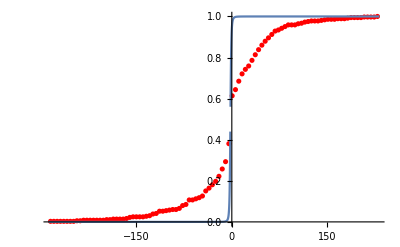

```mathematica
Show[ListPlot[d, PlotStyle->Red], Plot[ CDF[StudentTDistribution[2.912792001879522],x+2.1812170026093485],{x,-288, 232}]]
```

```mathematica
d//MatrixForm
```

(-284.905 | 0.00273973)